## CN Implicit Method Coding

CN: Crank-Nicolson

## Student Name: Roaa Tareq Mohammed Sec. 1 BN. 24

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

## Given Data

```mathematica
tmax = 1.08;
ymax = 0.04;
Δt = 0.01;
Δy = 0.001;
ΔtReq = 0.18;
u0 = 40;
ν = 0.000217;
```

## Initialization

```mathematica
t = Range[0,tmax,Δt];
y = Range[0,ymax,Δy];

tReq = Range[0,tmax,ΔtReq];

row =Length[y]; (*jm*)
col =Length[t]; (*nm*)

d = ν*Δt/Δy^2; 

tReqIndex = Range[1,col,18];

uReq = Array[0&,Length[tReqIndex]];

(*Matrices for the coefficients of system of equations*)
MatNp1 = Array[0&,{row-2,row-2}];
MatN = Array[0&,{row-2,row+2}];

(* Velocity vector at time station n*)
uN = Array[0&,row+2];     (*{Subscript[u, 1]^(n+1) Subscript[u, 1]^n Subscript[u, 2]^n ... Subscript[u, jm]^n Subscript[u, jm]^(n+1)}*)
uN[[1]] = 40;
uN[[2]] = 40;

(* Velocity vector at time station n+1*)
uNp1 = Array[0&,col-1];   (*{Subscript[u, 2]^(n+1) Subscript[u, 3]^(n+1) ... Subscript[u, jm-2]^(n+1) Subscript[u, jm-1]^(n+1)}*)

(* Velocity vector at all time stations*)
u = Array[0&,col];
```

## Array Construction

(Mat^(n+1))(u_2^n
u_3^n

(u_(jm-2))^n
(u_(jm-1))^n)=(Mat^n)(u_1^(n+1)
u_1^n

u_jm^n
u_jm^(n+1))

#### Mat^(n+1) construction

```mathematica
For[j=1,j<=row-2,j++,Which[j>1,MatNp1[[j,j-1]]=d];MatNp1[[j,j]]=-2*(1+d);
Which[j<row-2,MatNp1[[j,j+1]]=d]]
```

#### Mat^n construction

```mathematica
For[j=1,j<=row-2,j++,Which[j==1,MatN[[j,j]]=-d];MatN[[j,j+1]]=-d;MatN[[j,j+2]]=2*(d-1);
MatN[[j,j+3]]=-d;Which[j==row-2,MatN[[j,j+4]]=-d]]
```

## Velocity Computation

```mathematica
For[n=1,n<col,n++,uNp1[[n]]=Inverse[MatNp1].MatN.uN;u[[n]] = uN[[2;;Length[uN]-1]]; 
uN[[3;;Length[uN]-2]] = uNp1[[n]];Which[n==col-1,u[[n+1]] = uN[[2;;Length[uN]-1]]]]

uReq = u[[tReqIndex[[#]]]] &/@ Range[1,Length[tReqIndex]];
```

## Table of u(t,y)

```mathematica
tLabel = "t = " <> ToString[#]<> " s"&/@tReq;
yLabel = "y = " <> ToString[#]<> " m"&/@y;

TableForm[uReq[[#]]&/@Range[1,Length[tReqIndex]],
TableDirections->Row,TableHeadings->{tLabel ,yLabel},TableSpacing->{1, 0.5}]
```

| t = 0. s | t = 0.18 s | t = 0.36 s | t = 0.54 s | t = 0.72 s | t = 0.9 s | t = 1.08 s
y = 0. m | 40 | 40 | 40 | 40 | 40 | 40 | 40
y = 0.001 m | 0 | 36.3964 | 37.449 | 37.9164 | 38.1952 | 38.3848 | 38.523
y = 0.002 m | 0 | 32.8392 | 34.9144 | 35.8418 | 36.3961 | 36.7736 | 37.0491
y = 0.003 m | 0 | 29.3712 | 32.412 | 33.7847 | 34.6085 | 35.1707 | 35.5812
y = 0.004 m | 0 | 26.0346 | 29.9572 | 31.7539 | 32.838 | 33.5798 | 34.1225
y = 0.005 m | 0 | 22.864 | 27.5645 | 29.7574 | 31.0899 | 32.0051 | 32.6757
y = 0.006 m | 0 | 19.8904 | 25.2473 | 27.8031 | 29.3696 | 30.4501 | 31.2438
y = 0.007 m | 0 | 17.1365 | 23.0174 | 25.8983 | 27.6819 | 28.9186 | 29.8294
y = 0.008 m | 0 | 14.6187 | 20.8852 | 24.0495 | 26.0316 | 27.4139 | 28.4353
y = 0.009 m | 0 | 12.346 | 18.8596 | 22.2627 | 24.4229 | 25.9394 | 27.0639
y = 0.01 m | 0 | 10.3206 | 16.9474 | 20.5434 | 22.8597 | 24.498 | 25.7174
y = 0.011 m | 0 | 8.53844 | 15.1538 | 18.8958 | 21.3456 | 23.0924 | 24.3981
y = 0.012 m | 0 | 6.99028 | 13.4822 | 17.3238 | 19.8837 | 21.7251 | 23.1078
y = 0.013 m | 0 | 5.66241 | 11.9342 | 15.8303 | 18.4765 | 20.3983 | 21.8484
y = 0.014 m | 0 | 4.53791 | 10.5099 | 14.4173 | 17.1264 | 19.1139 | 20.6215
y = 0.015 m | 0 | 3.59766 | 9.20757 | 13.0862 | 15.8351 | 17.8735 | 19.4282
y = 0.016 m | 0 | 2.8214 | 8.02448 | 11.8376 | 14.6037 | 16.6784 | 18.2699
y = 0.017 m | 0 | 2.18858 | 6.95652 | 10.6713 | 13.4332 | 15.5296 | 17.1473
y = 0.018 m | 0 | 1.67917 | 5.99863 | 9.58644 | 12.3239 | 14.4277 | 16.0611
y = 0.019 m | 0 | 1.27423 | 5.14491 | 8.58159 | 11.2757 | 13.373 | 15.0118
y = 0.02 m | 0 | 0.956356 | 4.38887 | 7.65474 | 10.2882 | 12.3657 | 13.9995
y = 0.021 m | 0 | 0.709912 | 3.72357 | 6.80336 | 9.36046 | 11.4054 | 13.0241
y = 0.022 m | 0 | 0.521207 | 3.14184 | 6.02452 | 8.49132 | 10.4917 | 12.0856
y = 0.023 m | 0 | 0.378484 | 2.63638 | 5.31491 | 7.67919 | 9.62359 | 11.1832
y = 0.024 m | 0 | 0.271854 | 2.19997 | 4.67092 | 6.92221 | 8.80012 | 10.3164
y = 0.025 m | 0 | 0.193151 | 1.82553 | 4.08872 | 6.21821 | 8.01992 | 9.48418
y = 0.026 m | 0 | 0.135758 | 1.50626 | 3.5643 | 5.56478 | 7.2814 | 8.68546
y = 0.027 m | 0 | 0.0944002 | 1.2357 | 3.09354 | 4.95931 | 6.58276 | 7.91892
y = 0.028 m | 0 | 0.0649476 | 1.00781 | 2.67226 | 4.39896 | 5.92197 | 7.18306
y = 0.029 m | 0 | 0.0442162 | 0.816973 | 2.29623 | 3.88074 | 5.29685 | 6.47619
y = 0.03 m | 0 | 0.0297904 | 0.658048 | 1.96127 | 3.40151 | 4.705 | 5.7965
y = 0.031 m | 0 | 0.0198651 | 0.526364 | 1.66324 | 2.95802 | 4.1439 | 5.142
y = 0.032 m | 0 | 0.0131114 | 0.417708 | 1.39806 | 2.5469 | 3.61085 | 4.51056
y = 0.033 m | 0 | 0.00856468 | 0.328307 | 1.16173 | 2.16471 | 3.10306 | 3.89994
y = 0.034 m | 0 | 0.00553431 | 0.254799 | 0.950365 | 1.80795 | 2.6176 | 3.30778
y = 0.035 m | 0 | 0.00353189 | 0.194193 | 0.760168 | 1.47307 | 2.15145 | 2.73164
y = 0.036 m | 0 | 0.00221568 | 0.143822 | 0.587438 | 1.15646 | 1.70152 | 2.16896
y = 0.037 m | 0 | 0.0013481 | 0.101299 | 0.428563 | 0.854499 | 1.26465 | 1.61714
y = 0.038 m | 0 | 0.000763514 | 0.0644628 | 0.280008 | 0.563545 | 0.837616 | 1.07352
y = 0.039 m | 0 | 0.000343898 | 0.031322 | 0.138298 | 0.279935 | 0.41716 | 0.535385
y = 0.04 m | 0 | 0 | 0 | 0 | 0 | 0 | 0

## Plot of the velocity profiles y versus u for various t

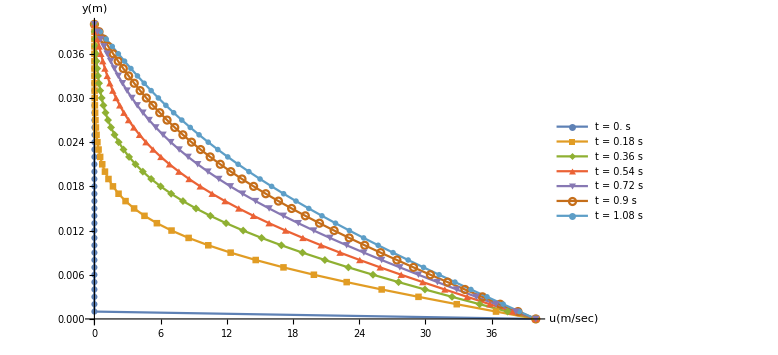

```mathematica
plots =MapThread[{#1,#2}&,{uReq[[#]],y}]&/@Range[1,Length[uReq]];
ListLinePlot[plots, PlotMarkers->Automatic,PlotLegends->tLabel ,AxesLabel->{"u(m/sec)","y(m)"},ImageSize->Large]
```

## Analytical Solution

```mathematica
Exact = Array[0&,{row, Length[tReq]}];
For[v=2,v<=Length[tReq],v++,
η=y/(2 √(ν·tReq[[v]]));
η1=ymax/(2 √(ν·tReq[[v]]));
Exact[[All,v]] = u0*(∑_(n=0)^1000 Erfc[2*n*η1+η]-∑_(n=0)^1000 Erfc[2*(n+1)*η1-η])]
ErrorContainer = (Transpose[uReq][[1;;row-1,2;;Length[tReq]]]-Exact[[1;;row-1,2;;Length[tReq]]])/Exact[[1;;row-1,2;;Length[tReq]]]*100;
```